```mathematica
zero={{0,0},{0,0}};
```

{{0,0},{0,0}}

```mathematica
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero},{zero,ⅈ PauliMatrix[2]}}];
```

```mathematica
A=DiagonalMatrix[{a,a}];
B=DiagonalMatrix[{b,b}];
Cc=DiagonalMatrix[{cp,cm}];
```

```mathematica
(σ[a_,b_,cp_,cm_]=ArrayFlatten[{{A,Cc},{Cc,B}}])//MatrixForm
```

(a | 0 | cp | 0
0 | a | 0 | cm
cp | 0 | b | 0
0 | cm | 0 | b)

```mathematica
s=Table[RandomReal[{1,10}],{i,10^3}];
d=Table[RandomReal[{1-s[[i]],s[[i]]-1}],{i,10^3}];
g=Table[RandomReal[{2 Abs[d[[i]]]+1,100}],{i,10^3}];
λ=Table[RandomReal[{-1,1}],{i,10^3}];

a=Table[s[i]+d[i],{i,10^3}];
b=Table[s[i]-d[i],{i,10^3}];

cp=Table[
[1/[4sqrt[[s[i]]^2-[d[i]]^2]]]*[[sqrt[[4[d[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]-4[g[i]]^2]+[sqrt[4[s[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]]
,{i,10^3}];

cm=Table[
[1/[4sqrt[[s[i]]^2-[d[i]]^2]]]*[[sqrt[[4[d[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]-4[g[i]]^2]-[sqrt[4[s[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]]
,{i,10^3}];
```

```mathematica
s[[1]]
```

8.23936

```mathematica
d[[1]]
```

1.89631

```mathematica
a[[1]];
```

```mathematica
b[[1]];
```

```mathematica
covm=Table[σ[a[i],b[i],cp[i],cm[i]],{i,10^3}];
```

```mathematica
covm[[4]]
```

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Min[Eigenvalues[covm[[i]]]],Min[Eigenvalues[covm[[i]]+ⅈ Σ]],Min[Abs[Eigenvalues[ⅈ Σ . covm[[i]]]//Chop]]}];,{i,1,Length[covm]}]
```

```mathematica
Length[phystest]
```

10000

```mathematica
phystest[[560]]
```

{0.546685,0.399842,1.98739}

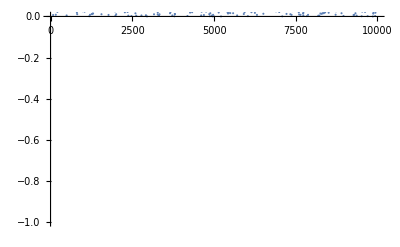

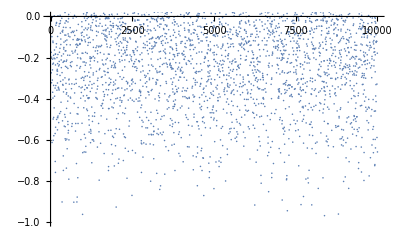

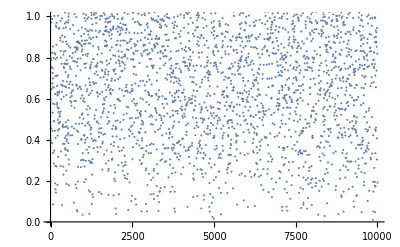

```mathematica
ListPlot[Table[phystest[[i,1]],{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[phystest[[i,2]],{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[phystest[[i,3]],{i,1,Length[cm]}],PlotRange->{0,1}]
```

```mathematica
Clear[cm]
```

```mathematica
Eigenvalues[σ[a,b,cp,cm]]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+4 cm^2)),1/2 (a+b+√((a-b)^2+4 cm^2)),1/2 (a+b-√((a-b)^2+4 cp^2)),1/2 (a+b+√((a-b)^2+4 cp^2))}

```mathematica
Eigenvalues[σ[a,b,cp,cm]+ⅈ Σ]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2))))}

```mathematica
Eigenvalues[ⅈ Σ . σ[a,b,cp,cm]]//FullSimplify
```

{-(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),-(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2)}